#### Задание 5

Решение задачи графическим методом
Вариант 15

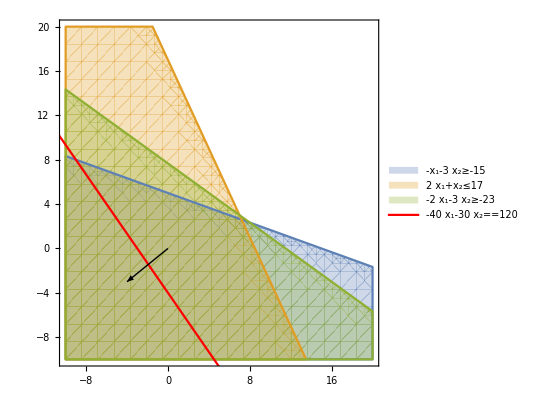

```mathematica
Show[RegionPlot[{-Subscript[x, 1]-3 Subscript[x, 2]≥-15, 2 Subscript[x, 1]+Subscript[x, 2]≤17,-2 Subscript[x, 1]-3 Subscript[x, 2]≥-23} ,{Subscript[x, 1], -10, 20},{Subscript[x, 2], -10, 20},PlotLegends->"Expressions"],
ContourPlot[-40 Subscript[x, 1]-30 Subscript[x, 2]==120,{Subscript[x, 1], -15, 20},{Subscript[x, 2], -15, 20},ContourStyle->Red,PlotLegends->"AllExpressions"],
Graphics@Arrow[{{0,0},{-4,-3}}], 
Axes->True]
```

```mathematica
point = First@Solve[-Subscript[x, 1]-3 Subscript[x, 2]==-15&& 2 Subscript[x, 1]+Subscript[x, 2]==17,{Subscript[x, 1],Subscript[x, 2]}]
```

{x_1→36/5,x_2→13/5}

```mathematica
minL=(-40 Subscript[x, 1]-30 Subscript[x, 2])/.point
```

-366

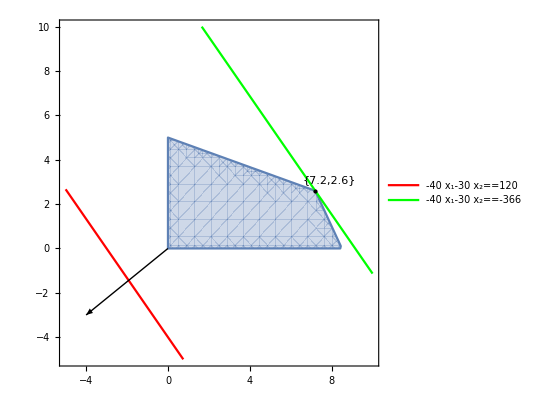

```mathematica
Show[RegionPlot[-Subscript[x, 1]-3 Subscript[x, 2]≥-15&& 2 Subscript[x, 1]+Subscript[x, 2]≤17&&-2 Subscript[x, 1]-3 Subscript[x, 2]≥-23 &&Subscript[x, 1]≥0&&Subscript[x, 2]≥0,{Subscript[x, 1], -5, 10},{Subscript[x, 2], -5, 10}],
ContourPlot[-40 Subscript[x, 1]-30 Subscript[x, 2]==120,{Subscript[x, 1], -5, 10},{Subscript[x, 2], -5, 10},ContourStyle->Red,PlotLegends->"AllExpressions"],
ContourPlot[-40 Subscript[x, 1]-30 Subscript[x, 2]==minL,{Subscript[x, 1], -5, 10},{Subscript[x, 2], -5, 10},ContourStyle->Green,PlotLegends->"AllExpressions"],
Graphics[Arrow[{{0,0},{-4,-3}}]],
Graphics[{Point[point⟦All,2⟧],Text[N@point⟦All,2⟧,point⟦All,2⟧+{0.7,0.5}]}], 
Axes->True]
```